quad diagram

```mathematica
Quit[]
```

```mathematica
g=9.81;
numericProblemConstants=(*geometric properties:*)
{Subscript[L0, 1]=1,
Subscript[l, 2]=Subscript[L0, 1],
Subscript[k, 1]=200.,
Subscript[k, 2]=Subscript[k, 1],
Subscript[w, p]=Subscript[L0, 1]/2, (* half of the length of payload box Normalized by Subscript[L0, 1] *)
Subscript[h, p]=Subscript[L0, 1]/2/10, (* half of the hight of payload box Normalized by -"- *)
Subscript[m, p]=1,Subscript[m, 1]=1,Subscript[m, 2]=1, (* [kg] *)
};
initialLocations=
{Subscript[x, 1]=0,Subscript[y, 1]=0,Subscript[x, 2]=2 Subscript[w, p],Subscript[y, 2]=0,Subscript[x, p]=Subscript[w, p],Subscript[y, p]=-Subscript[L0, 1]-Subscript[h, p]-g/Subscript[L0, 1] Subscript[m, p]/Subscript[k, 1],Subscript[θ, p]=0 Degree};
```

```mathematica
(*numericProblemConstants=(*geometric properties:*)
{Subscript[L0, 1]=1}*)
```

{1}

```mathematica
Clear["x_p"]
Clear["x"]
?x
```

Global`x

```mathematica
?Subscript[y, p]
```

Information::ssym: y_p is not a symbol or a valid string pattern.

Information[y_p,LongForm→False]

```mathematica
?xp
```

Global`xp

```mathematica
Clear[DrawSystem]
```

```mathematica
DrawSystem[x1_,y1_,x2_,y2_,xp_,yp_,θp_,wp_]:=(*Block[{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],Subscript[θ, p]},*){
(*(* locations:*)
{Subscript[x, 1]=x1,Subscript[y, 1]=y1,
Subscript[x, 2]=x2,Subscript[y, 2]=y2,
Subscript[x, p]=xp,Subscript[y, p]=yp,Subscript[θ, p]=θp Degree};*)
(*Orientation*)
(Rp2I=(RotationMatrix[θp]))//MatrixForm;
(*locations:*)
{Iorigin={x1,y1},
sizeFactor=Subscript[L0, 1]*0.75;
IaxisX = {x1,y1+1*sizeFactor},
IaxisY = {x1+1*sizeFactor,y1},
Quad1CenterPos = {x1,y1},
Quad2CenterPos = {x2,y2},
PayloadCenterPos = {xp,yp},
HangPoint1=PayloadCenterPos+Rp2I.{-wp,+Subscript[h, p]},
HangPoint2=PayloadCenterPos+Rp2I.{+wp,+Subscript[h, p]}};
(*labels*)
PayloadLabel =Text["Payload",{xp,yp},{-2,4}+Rp2I.{-wp,Subscript[h, p]}]; (*down and right offset*)
Quad1Label =Text["Quad1",{x1,y1},{-1,-1}];
Quad2Label =Text["Quad2",{x2,y2},{-1,-1}];
l1Label=Text["L0_1",{(x1+xp)/2,(y1+yp)/2},{-2,1}];
l2Label=Text["L0_2",{(x2+xp)/2,(y2+yp)/2},{2,1}];
(*general additions *)
spring[r_: {1,0},n_: 20,w_: 1,origin_:{0,0}]:=Line@Transpose[{r-origin,-Cross[r-origin]}.{(#-1)/(2 n),Re[I^#] w/Norm[r-origin]}+origin]&@Range[2 n+1];
(*elements:*)
Iarrows={Dashed,Arrowheads[Small],Arrow[{Iorigin,IaxisX}],Arrow[{Iorigin,IaxisY}]};
Labels = {PayloadLabel,Quad1Label,Quad2Label,l1Label,l2Label};
Cabels ={Arrowheads[{-Small,Small}],Arrow[{HangPoint1,Quad1CenterPos}],Arrow[{HangPoint2,Quad2CenterPos}]};
(*spr1=spring[r/.r->HangPoint1+{-1,1},n/.n->8,w/.w->1/3.,origin/.origin->Quad1Pos+{-1,-1}];*)
spr1=spring[r/.r->HangPoint1,n/.n->8,1/3.,origin/.origin->Quad1CenterPos];
spr2=spring[HangPoint2,8,1/3,Quad2CenterPos];
(*PayloadBox={Rotate[Rectangle[HangPoint1-Rp2I.{0,Subscript[h, p]},HangPoint2],-θp]};
PayloadBoxRef={Rotate[Rectangle[HangPoint1-Rp2I.{0,Subscript[h, p]},HangPoint2],0]};
*)
(*PayloadBox={Rotate[Rectangle[PayloadCenterPos-{wp,Subscript[h, p]},PayloadCenterPos+{wp,Subscript[h, p]}],θp]};
Print[θp];Print[wp];*)
PayloadBox={Rotate[Rectangle[PayloadCenterPos-{wp,Subscript[h, p]},PayloadCenterPos+{wp,Subscript[h, p]}],θp]};
If[wp>0,
Print[θp];Print["wp poistive indeed. depends on the function called method.."];
PayloadBox={Rotate[Rectangle[PayloadCenterPos-{wp,Subscript[h, p]},PayloadCenterPos+{wp,Subscript[h, p]}],θp]},
PayloadBox={Circle[PayloadCenterPos,Subscript[L0, 1]/2]}];
(*a=*)Graphics[{Iarrows,Labels,Cabels,spr1,spr2,PayloadBox}] }
{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],Subscript[θ, p]}
{Subscript[w, p],Subscript[h, p]}
DrawSystem[Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],0];
```

{x_1,y_1,x_2,y_2,x_p,y_p,θ_p}

{w_p,h_p}

```mathematica
man = Manipulate[DrawSystem[Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],θp,Subscript[w, p]][[1]]/.{Subscript[x, p]->Subscript[w, p],Subscript[y, p]->-Subscript[L0, 1]-Subscript[h, p]-g/Subscript[L0, 1] Subscript[m, p]/Subscript[k, 1]}/.NumericParametersTest,
{{Subscript[x, 1],0,"x_1"},-Subscript[L0, 1],Subscript[L0, 1]},
{{Subscript[x, 2],2 Subscript[w, p],"x_2"},2 Subscript[w, p]+-Subscript[L0, 1],2 Subscript[w, p]+Subscript[L0, 1]},
{{Subscript[y, 1],0,"y_1"},-Subscript[L0, 1],Subscript[L0, 1]},
{{Subscript[y, 2],0,"y_2"},-Subscript[L0, 1],Subscript[L0, 1]},
{{θp,0,"θ_p"},-90Degree,90.Degree}
]//.NumericParametersTest
```

0

wp poistive indeed. depends on the function called method..

ReplaceAll::reps: {NumericParametersTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

wp poistive indeed. depends on the function called method..

ReplaceAll::reps: {NumericParametersTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

wp poistive indeed. depends on the function called method..

ReplaceAll::reps: {NumericParametersTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

wp poistive indeed. depends on the function called method..

ReplaceAll::reps: {NumericParametersTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

wp poistive indeed. depends on the function called method..

ReplaceAll::reps: {NumericParametersTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
imQuad=Import["C:\\Users\\Ran_the_User\\Documents\\GitHub\\quad_docs\\web examples\\3dquad.png"]
```

-Graphics-

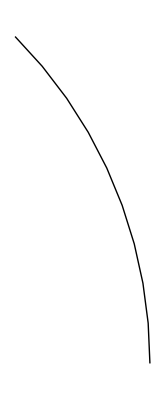

```mathematica
Graphics[Circle[{0,0},1,{0, Pi/4}]]
```

```mathematica
ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"test.avi"}],man],"ImageList"][[1;;-1;;step]]];

ManToGif[man,FileNameJoin[{NotebookDirectory[],"test"}],1];
```